```mathematica
allGraphs4[271,"graph"]
```

-Graphics-

```mathematica
allGraphs4AtomKeysSorted=Sort[allGraphs4AtomKeys,CompareSymbols[allGraphs4[#1,"colofour"],allGraphs4[#2,"colofour"]]&];
```

```mathematica
allGraphs4NullAtomKeysSorted=Sort[allGraphs4NullAtomKeys,CompareSymbols[allGraphs4[#1,"colofourrealnull"],allGraphs4[#2,"colofourrealnull"]]&];
```

```mathematica
Vector4[key_]:=Table[Coefficient[allGraphs4[key,"colofourrealnull"],allGraphs4[k,"colofourrealnull"]],{k, allGraphs4NullAtomKeysSorted}]
```

```mathematica
Vector4Full[key_]:=Table[Coefficient[allGraphs4[key,"colofour"],allGraphs4[k,"colofour"]],{k, allGraphs4AtomKeysSorted}]
```

```mathematica
TableForm[{Table[allGraphs4[k,"colofourrealnull"],{k,allGraphs4NullAtomKeysSorted}],Vector4Full[93],Vector4[93],Vector4Full[271],Vector4[271]}, TableDirections->Row,TableHeadings->{{"","Full"allGraphs4[93,"graph"],"Empty" allGraphs4[93,"graph"],"Full" allGraphs4[271,"graph"],"Empty" allGraphs4[271,"graph"]}, Table[allGraphs4[k,"colofour"],{k, allGraphs4AtomKeysSorted}]}]
```

|  | -Graphics- Full | -Graphics- Empty | -Graphics- Full | -Graphics- Empty
v1x2x3x4 | n1x2x3x4 | 1 | 1 | 1 | 1
v1x2x34 | n1x2x34 | 1 | 0 | 0 | -1
v1x23x4 | n1x23x4 | 0 | -1 | 1 | 0
v1x24x3 | n1x24x3 | 0 | -1 | 1 | 0
v12x3x4 | n12x3x4 | 1 | 0 | 0 | -1
v13x2x4 | n13x2x4 | 0 | -1 | 1 | 0
v14x2x3 | n14x2x3 | 1 | 0 | 0 | -1
v1x234 | n1x234 | 0 | 1 | 0 | 0
v12x34 | n12x34 | 1 | 0 | 0 | 1
v123x4 | n123x4 | 0 | 1 | 0 | 0
v124x3 | n124x3 | 0 | 0 | 0 | 1
v13x24 | n13x24 | 0 | 1 | 1 | 0
v134x2 | n134x2 | 0 | 0 | 0 | 1
v14x23 | n14x23 | 0 | 0 | 0 | 0
v1234 | n1234 | 0 | -1 | 0 | -1

```mathematica
MobiusGraphDoubleGreen2[key_,key2_,key3_,allGraphs_]:=Block[{
form=allGraphs[key,"colofourrealnull"],
form2=allGraphs[key2, "colofourrealnull"],
form3=Map[ChangeSymbol[#]&,allGraphs[key2,"colofour"]],
pairs, 
vars, 
blocks=Association[],
c,
edges,
edges2,
set, 
found=Association[],
mob,
mob2,
realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]],
nonRoot,

 bondGraphs,
 sublattice},

vars=ListofVars[form];
Table[blocks[k]={},{k,0,6}];
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}];
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,6}];
pairs=Subsets[ListofVars[form3],{2}];
edges2={};
Table[With[{e=DirectedEdge[
p[[2]],
p [[1]]]},
If[MemberQ[edges,e],edges2=Append[edges2,e]]],{p,pairs}
];
mob=MobiusGraph4[key2,allGraphs];
mob2=MobiusGraph4[key3,allGraphs];
nonRoot=Select[VertexList[mob],VertexInDegree[mob,#]>0&];
sublattice=mob;
bondGraphs=Association[Map[#->allGraphs[ CalcSubGraph[sublattice,#,allGraphs],"graph"]&,VertexList[sublattice]]];
Graph[vars,edges,VertexLabels->Table[n->StringReplace[StringDrop[SymbolName[n],1],"x"->"|"],{n,vars}],GraphLayout->"LayeredDigraphEmbedding",
EdgeStyle->Map[#->Darker[Green]&,EdgeList[mob2]],
VertexStyle->Map[#->Darker[Green]&,VertexList[mob2]],
GraphHighlight->Join[VertexList[mob],EdgeList[mob]],
ImageSize->720]
]
```

```mathematica
Select[Keys[allGraphs4],With[{g=allGraphs4[#,"graph"]},VertexCount[g]==4 && EdgeCount[g]==3&&EdgeQ[g,1<->3]&&EdgeQ[g,3<->2]&&EdgeQ[g,4<->2]
]&]
```

{93}

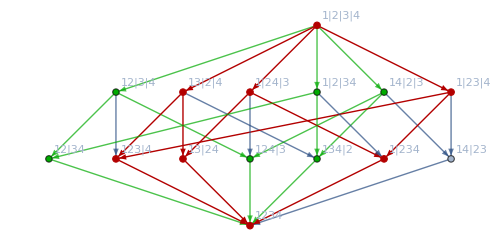

```mathematica
Show[MobiusGraphDoubleGreen2[K4Key,93,271,allGraphs4],ImageSize->500]
```

```mathematica
FindComplement[key_,allGraphs_]:=Block[{compl, g, rest},
g=allGraphs[key,"graph"];
compl=GraphComplement[g];
rest=Select[allGraphs,#["vertexsets"]==allGraphs[key,"vertexsets"]&];
rest=Select[rest,VertexCount[#["graph"]]==VertexCount[compl]&&EdgeCount[#["graph"]]==EdgeCount[compl]&];
Table[
rest=Select[rest,EdgeQ[#["graph"],e]&]
,{e,EdgeList[compl]}
];
First[Keys[rest]]
]
```

```mathematica
FindComplement[271,allGraphs4]
```

93

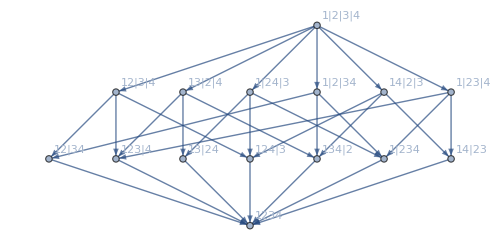
{-Graphics-
v1234+v123x4+v124x3+v12x34+v12x3x4+v134x2+v13x24+v13x2x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4
v1x2x3x4-Graphics-0→-Graphics-364,-Graphics-
v134x2+v13x24+v13x2x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4
v12x3x4+v1x2x3x4-Graphics-243→-Graphics-121,-Graphics-
v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4
v12x3x4+v13x2x4+v1x2x3x4-Graphics-324→-Graphics-40,-Graphics-
v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4
v12x3x4+v13x2x4+v14x2x3+v1x2x3x4-Graphics-351→-Graphics-13,-Graphics-
v1x24x3+v1x2x34+v1x2x3x4
v123x4+v12x3x4+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x3x4-Graphics-360→-Graphics-4,-Graphics-
v1x2x34+v1x2x3x4
v123x4+v124x3+v12x3x4+v13x24+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4-Graphics-363→-Graphics-1,-Graphics-
v1x2x3x4
v1234+v123x4+v124x3+v12x34+v12x3x4+v134x2+v13x24+v13x2x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4-Graphics-364→-Graphics-0,-Graphics-
v1x24x3+v1x2x3x4
v123x4+v12x34+v12x3x4+v134x2+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4-Graphics-361→-Graphics-3,-Graphics-
v1x23x4+v1x2x34+v1x2x3x4
v124x3+v12x3x4+v13x24+v13x2x4+v14x2x3+v1x24x3+v1x2x3x4-Graphics-354→-Graphics-10,-Graphics-
v1x23x4+v1x2x3x4
v124x3+v12x34+v12x3x4+v134x2+v13x24+v13x2x4+v14x2x3+v1x24x3+v1x2x34+v1x2x3x4-Graphics-355→-Graphics-9,-Graphics-
v1x23x4+v1x24x3+v1x2x3x4
v12x34+v12x3x4+v134x2+v13x2x4+v14x2x3+v1x2x34+v1x2x3x4-Graphics-352→-Graphics-12,-Graphics-
v14x2x3+v1x24x3+v1x2x34+v1x2x3x4
v123x4+v12x3x4+v13x2x4+v1x23x4+v1x2x3x4-Graphics-333→-Graphics-31,-Graphics-
v14x2x3+v1x2x34+v1x2x3x4
v123x4+v12x3x4+v13x24+v13x2x4+v1x23x4+v1x24x3+v1x2x3x4-Graphics-336→-Graphics-28,-Graphics-
v14x2x3+v1x2x3x4
v123x4+v12x34+v12x3x4+v13x24+v13x2x4+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4-Graphics-337→-Graphics-27,-Graphics-
v14x2x3+v1x24x3+v1x2x3x4
v123x4+v12x34+v12x3x4+v13x2x4+v1x23x4+v1x2x34+v1x2x3x4-Graphics-334→-Graphics-30,-Graphics-
v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4
v12x3x4+v13x24+v13x2x4+v1x24x3+v1x2x3x4-Graphics-327→-Graphics-37,-Graphics-
v14x23+v14x2x3+v1x23x4+v1x2x3x4
v12x34+v12x3x4+v13x24+v13x2x4+v1x24x3+v1x2x34+v1x2x3x4-Graphics-328→-Graphics-36,-Graphics-
v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4
v12x34+v12x3x4+v13x2x4+v1x2x34+v1x2x3x4-Graphics-325→-Graphics-39,-Graphics-
v13x24+v13x2x4+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4
v12x3x4+v14x2x3+v1x2x3x4-Graphics-270→-Graphics-94,-Graphics-
v13x24+v13x2x4+v1x24x3+v1x2x34+v1x2x3x4
v12x3x4+v14x23+v14x2x3+v1x23x4+v1x2x3x4-Graphics-279→-Graphics-85,-Graphics-
v13x2x4+v1x2x34+v1x2x3x4
v124x3+v12x3x4+v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4-Graphics-282→-Graphics-82,-Graphics-
v13x2x4+v1x2x3x4
v124x3+v12x34+v12x3x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4-Graphics-283→-Graphics-81,-Graphics-
v13x24+v13x2x4+v1x24x3+v1x2x3x4
v12x34+v12x3x4+v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4-Graphics-280→-Graphics-84,-Graphics-
v13x2x4+v1x23x4+v1x2x34+v1x2x3x4
v124x3+v12x3x4+v14x2x3+v1x24x3+v1x2x3x4-Graphics-273→-Graphics-91,-Graphics-
v13x2x4+v1x23x4+v1x2x3x4
v124x3+v12x34+v12x3x4+v14x2x3+v1x24x3+v1x2x34+v1x2x3x4-Graphics-274→-Graphics-90,-Graphics-
v13x24+v13x2x4+v1x23x4+v1x24x3+v1x2x3x4
v12x34+v12x3x4+v14x2x3+v1x2x34+v1x2x3x4-Graphics-271→-Graphics-93,-Graphics-
v134x2+v13x24+v13x2x4+v14x2x3+v1x24x3+v1x2x34+v1x2x3x4
v12x3x4+v1x23x4+v1x2x3x4-Graphics-252→-Graphics-112,-Graphics-
v134x2+v13x2x4+v14x2x3+v1x2x34+v1x2x3x4
v12x3x4+v1x23x4+v1x24x3+v1x2x3x4-Graphics-255→-Graphics-109,-Graphics-
v13x2x4+v14x2x3+v1x2x3x4
v12x34+v12x3x4+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4-Graphics-256→-Graphics-108,-Graphics-
v13x24+v13x2x4+v14x2x3+v1x24x3+v1x2x3x4
v12x34+v12x3x4+v1x23x4+v1x2x34+v1x2x3x4-Graphics-253→-Graphics-111,-Graphics-
v134x2+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4
v12x3x4+v1x24x3+v1x2x3x4-Graphics-246→-Graphics-118,-Graphics-
v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x3x4
v12x34+v12x3x4+v1x24x3+v1x2x34+v1x2x3x4-Graphics-247→-Graphics-117,-Graphics-
v13x24+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4
v12x34+v12x3x4+v1x2x34+v1x2x3x4-Graphics-244→-Graphics-120,-Graphics-
v124x3+v12x34+v12x3x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4
v13x2x4+v1x2x3x4-Graphics-81→-Graphics-283,-Graphics-
v12x34+v12x3x4+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4
v13x2x4+v14x2x3+v1x2x3x4-Graphics-108→-Graphics-256,-Graphics-
v12x34+v12x3x4+v1x24x3+v1x2x34+v1x2x3x4
v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x3x4-Graphics-117→-Graphics-247,-Graphics-
v12x34+v12x3x4+v1x2x34+v1x2x3x4
v13x24+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4-Graphics-120→-Graphics-244,-Graphics-
v12x3x4+v1x2x3x4
v134x2+v13x24+v13x2x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4-Graphics-121→-Graphics-243,-Graphics-
v12x3x4+v1x24x3+v1x2x3x4
v134x2+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4-Graphics-118→-Graphics-246,-Graphics-
v12x34+v12x3x4+v1x23x4+v1x2x34+v1x2x3x4
v13x24+v13x2x4+v14x2x3+v1x24x3+v1x2x3x4-Graphics-111→-Graphics-253,-Graphics-
v12x3x4+v1x23x4+v1x2x3x4
v134x2+v13x24+v13x2x4+v14x2x3+v1x24x3+v1x2x34+v1x2x3x4-Graphics-112→-Graphics-252,-Graphics-
v12x3x4+v1x23x4+v1x24x3+v1x2x3x4
v134x2+v13x2x4+v14x2x3+v1x2x34+v1x2x3x4-Graphics-109→-Graphics-255,-Graphics-
v124x3+v12x34+v12x3x4+v14x2x3+v1x24x3+v1x2x34+v1x2x3x4
v13x2x4+v1x23x4+v1x2x3x4-Graphics-90→-Graphics-274,-Graphics-
v12x34+v12x3x4+v14x2x3+v1x2x34+v1x2x3x4
v13x24+v13x2x4+v1x23x4+v1x24x3+v1x2x3x4-Graphics-93→-Graphics-271,-Graphics-
v12x3x4+v14x2x3+v1x2x3x4
v13x24+v13x2x4+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4-Graphics-94→-Graphics-270,-Graphics-
v124x3+v12x3x4+v14x2x3+v1x24x3+v1x2x3x4
v13x2x4+v1x23x4+v1x2x34+v1x2x3x4-Graphics-91→-Graphics-273,-Graphics-
v12x34+v12x3x4+v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4
v13x24+v13x2x4+v1x24x3+v1x2x3x4-Graphics-84→-Graphics-280,-Graphics-
v12x3x4+v14x23+v14x2x3+v1x23x4+v1x2x3x4
v13x24+v13x2x4+v1x24x3+v1x2x34+v1x2x3x4-Graphics-85→-Graphics-279,-Graphics-
v124x3+v12x3x4+v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4
v13x2x4+v1x2x34+v1x2x3x4-Graphics-82→-Graphics-282,-Graphics-
v123x4+v12x34+v12x3x4+v13x24+v13x2x4+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4
v14x2x3+v1x2x3x4-Graphics-27→-Graphics-337,-Graphics-
v12x34+v12x3x4+v13x24+v13x2x4+v1x24x3+v1x2x34+v1x2x3x4
v14x23+v14x2x3+v1x23x4+v1x2x3x4-Graphics-36→-Graphics-328,-Graphics-
v12x34+v12x3x4+v13x2x4+v1x2x34+v1x2x3x4
v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4-Graphics-39→-Graphics-325,-Graphics-
v12x3x4+v13x2x4+v1x2x3x4
v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4-Graphics-40→-Graphics-324,-Graphics-
v12x3x4+v13x24+v13x2x4+v1x24x3+v1x2x3x4
v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4-Graphics-37→-Graphics-327,-Graphics-
v123x4+v12x34+v12x3x4+v13x2x4+v1x23x4+v1x2x34+v1x2x3x4
v14x2x3+v1x24x3+v1x2x3x4-Graphics-30→-Graphics-334,-Graphics-
v123x4+v12x3x4+v13x2x4+v1x23x4+v1x2x3x4
v14x2x3+v1x24x3+v1x2x34+v1x2x3x4-Graphics-31→-Graphics-333,-Graphics-
v123x4+v12x3x4+v13x24+v13x2x4+v1x23x4+v1x24x3+v1x2x3x4
v14x2x3+v1x2x34+v1x2x3x4-Graphics-28→-Graphics-336,-Graphics-
v124x3+v12x34+v12x3x4+v134x2+v13x24+v13x2x4+v14x2x3+v1x24x3+v1x2x34+v1x2x3x4
v1x23x4+v1x2x3x4-Graphics-9→-Graphics-355,-Graphics-
v12x34+v12x3x4+v134x2+v13x2x4+v14x2x3+v1x2x34+v1x2x3x4
v1x23x4+v1x24x3+v1x2x3x4-Graphics-12→-Graphics-352,-Graphics-
v12x3x4+v13x2x4+v14x2x3+v1x2x3x4
v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4-Graphics-13→-Graphics-351,-Graphics-
v124x3+v12x3x4+v13x24+v13x2x4+v14x2x3+v1x24x3+v1x2x3x4
v1x23x4+v1x2x34+v1x2x3x4-Graphics-10→-Graphics-354,-Graphics-
v123x4+v12x34+v12x3x4+v134x2+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4
v1x24x3+v1x2x3x4-Graphics-3→-Graphics-361,-Graphics-
v123x4+v12x3x4+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x3x4
v1x24x3+v1x2x34+v1x2x3x4-Graphics-4→-Graphics-360,-Graphics-
v123x4+v124x3+v12x3x4+v13x24+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4
v1x2x34+v1x2x3x4-Graphics-1→-Graphics-363}

```mathematica
Table[With[{c=FindComplement[k,allGraphs4]},
Labeled[
TableForm[{
Show[MobiusGraphDoubleGreen2[K4Key,k,c,allGraphs4],ImageSize->500],
allGraphs4[k,"colofour"],
allGraphs4[c,"colofour"]
}
],Labeled[allGraphs4[k,"graph"],k]->Labeled[allGraphs4[c,"graph"],c]]
],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]}]
```